Your Title Here

```mathematica
f1=203;
f2=303;
f3[x_]:=-2110*x^2-153*x+515;
f4[x_]:=-3829*x^2+4625*x-947;
f5[x_]:=-7097*x^2+14370*x-6648;
```

```mathematica
diagram=Show[
Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->{Thick,Black}]&@@@{{f3[x],{0,0.35}},{f4[x],{0.35,0.8}},{f5[x],{0.8,1}}},
Plot[Piecewise[{{f1,x<0.6},{f2,x>0.6}}],{x,0,1},PlotStyle->{Thickness@0.01,Blue}],
Graphics@{Thick,Line[{{0.6,100},{0.6,450}}],Text[Style["■",17,Red],{0.603,450}]},
PlotRange->{{0,1},{100,625}},PlotRangePadding->None,Axes->None,Frame->True,FrameLabel->{"mole fraction B","temperature (°C)"},LabelStyle->{17,Black},ImageSize->{425,400},AspectRatio->Full];
```

```mathematica
Manipulate[
Module[{Q1,Q2,data,py,trackheat,trackx},
Q1=heat+100;Q2=heat;
(*py=Sort[{Q1,Which[px<0.6,f1,px>0.6,f2,px==0.6,450],Q2}][[2]];*)
data=Sort[{Q1,Which[px<0.6,f1,px>0.6,f2,px==0.6,450],Q2}];
(*py=data[[If[heat<data[[2]],2,If[px==0.6∧heat<350,1,2]]]];*)
py=If[px==0.6,Nearest[data,heat][[1]],data[[2]]];

trackheat=AppendTo[list1,heat];
trackx=AppendTo[list2,px];

Column[{Show[diagram,Epilog->{PointSize@0.03,Point[{px,py}]}],
(*Sort[{Q1,Which[px<0.6,f1,px>0.6,f2,px==0.6,450],Q2}][[2]],*)py,data,trackheat,trackx
}]
],
Grid[{
{Control[{{px,0.2,"mole fraction B"},0,1,0.05,Appearance->"Labeled"}],
Button["reset to original conditions",{heat=20,list1={},list2={}}]},
{Control[{{heat,20,"heat added (kJ)"},0,550,1,Appearance->"Labeled"}],
Control[{{list1,{}},None}],
Control[{{list2,{}},None}]}
},Alignment->Left],
TrackedSymbols:>{heat,px},SaveDefinitions->True]
```

## Original Using Manipulate - with Suggested Pathway

```mathematica
Manipulate[
Module[{Q1,Q2,data,py},
Q1=heat+100;Q2=heat;
(*py=Sort[{Q1,Which[px<0.6,f1,px>0.6,f2,px==0.6,450],Q2}][[2]];*)
data=Sort[{Q1,Which[px<0.6,f1,px>0.6,f2,px==0.6,450],Q2}];
py=data[[2]];

Column[{Show[diagram,Epilog->{
Switch[path,
1,{{Thick,Dashed,Green,Arrowheads@{{0.06,0.15},{0.06,0.6},{0.06,0.8},{0.06,1}},Arrow[{{0.2,120},{0.2,550},{0.75,550},{0.75,150},{0.6,150},{0.6,500}}]},
Text[Style["STOP",17,Background->White],#,{-1.5,-1}]&/@{{0.2,f1},{0.6,450},{0.75,f2}}},
2,{{Thick,Dashed,Red,Arrowheads@{{0.06,0.15},{0.06,0.5},{0.06,1}},Arrow[{{0.2,120},{0.2,250},{0.6,250},{0.6,525}}]},
Text[Style["STOP",17,Background->White],#,{-1.5,-1}]&/@{{0.2,f1},{0.6,450}}},
3,{}],
{PointSize@0.03,Point[{px,py}]}
}],
Sort[{Q1,Which[px<0.6,f1,px>0.6,f2,px==0.6,450],Q2}][[2]],py,data
}]
],
Grid[{
{Control[{{px,0.2,"mole fraction B"},0,1,0.05,Appearance->"Labeled"}],
Button["reset to original conditions",heat=20]},
{Control[{{heat,20,"heat added (kJ)"},0,550,1,Appearance->"Labeled"}],
Control[{{path,1,"path"},{1->" works ",2->" wrong ",3->" none "},Setter}]}
},Alignment->Left],
SaveDefinitions->True]
```

## Original Using Manipulate

```mathematica
Manipulate[
Module[{Q1,Q2,py},
Q1=heat+100;Q2=heat;
py=Sort[{Q1,Which[px<0.6,f1,px>0.6,f2,px==0.6,450],Q2}][[2]];

Show[diagram,Epilog->{PointSize@0.03,Point[{px,py}]}]
],
Grid[{
{Control[{{px,0.2,"mole fraction B"},0,1,0.05,Appearance->"Labeled"}],
Button["reset to original conditions",heat=20]},
{Control[{{heat,20,"heat added (kJ)"},0,500,1,Appearance->"Labeled"}]}
},Alignment->Left],
SaveDefinitions->True]
```

## Set Up for Animate Using Manipulate

```mathematica
Manipulate[
Module[{T1,T2,py},
If[T<600,{T1=T;T2=T-100;},{T1=600-(T-600);T2=T1-100;}];
py[loc_]:=Piecewise[{{T1,T1<loc},{loc,loc≤T1∧loc≥T2},{T2,loc<T2}}];

Show[diagram,Epilog->{PointSize@0.03,Point[{0.2,py[f1]}],Point[{0.6,py[450]}],Point[{0.9,py[f2]}]}]
],
Grid[{
{Control[{{px,0.2,"mole fraction B"},0,1,0.05,Appearance->"Labeled"}],
Button["reset to original conditions",T=120]},
{Control[{{T,120,"heat added (kJ)"},120,1080,1,Appearance->"Labeled"}]}
},Alignment->Left],
SaveDefinitions->True]
```

```mathematica
(*Text[Style[Grid@{{"T =",T},{"T_1 =",T1},{"T_2 =",T2},{"py =",py},{Style[If[py==T1,"T_1","T_2"],Bold],SpanFromLeft}},18],{0.35,600},{0,1}]*)
```

## Use Animate

```mathematica
Animate[
Module[{T1,T2,py},
If[T<600,{T1=T;T2=T-100;},{T1=600-(T-600);T2=T1-100;}];
py[loc_]:=Piecewise[{{T1,T1<loc},{loc,loc≤T1∧loc≥T2},{T2,loc<T2}}];

Show[diagram,Epilog->{PointSize@0.03,Point[{0.2,py[f1]}],Point[{0.6,py[450]}],Point[{0.9,py[f2]}]}]
],
{T,120,1080},AnimationRepetitions->1,AnimationRate->70]
```

```mathematica
Length@Range[120,1080,25]
```

39

## Export as gif

```mathematica
Export["stack SSLE example Aug 24 - (2).gif",Table[
Module[{T1,T2,py},
If[T<600,{T1=T;T2=T-100;},{T1=600-(T-600);T2=T1-100;}];
py[loc_]:=Piecewise[{{T1,T1<loc},{loc,loc≤T1∧loc≥T2},{T2,loc<T2}}];

Show[diagram,Epilog->{PointSize@0.03,Point[{0.2,py[f1]}],Point[{0.6,py[450]}],Point[{0.9,py[f2]}]}]
],
{T,120,1080,10}]
]
```

stack SSLE example Aug 24 - (2).gif

## Show Path Option

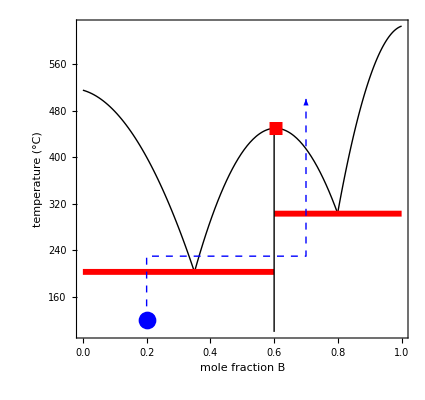





```mathematica
Show[diagram,Epilog->{Arrowheads@0.06,Thick,Dashed,Blue,Arrow[{{0.2,120},{0.2,230},{0.7,230},{0.7,500}}],PointSize@0.03,Point[{0.2,120}]}]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX